```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy452-basicstatmech"]

fs=Style[#,FontSize->14]&;
```

/Users/pjoot/project/figures/phy452-basicstatmech

```mathematica
Clear[f]

f[b_, l_] =  FullSimplify[D[ Sinh[b(l+1/2)]/Sinh[b/2], b]] ;
f[b, l] // TraditionalForm

f[b, 1] // FullSimplify
f[b, 2] // FullSimplify // Factor
f[b, 3] // FullSimplify // Factor
```

-1/2 csch^2(b/2) ((l+1) sinh(b l)-l sinh(b (l+1)))

2 Sinh[b]

2 (Sinh[b]+2 Sinh[2 b])

2 (Sinh[b]+2 Sinh[2 b]+3 Sinh[3 b])

```mathematica
TrigExpand[ Sinh[x + 1] - Sinh[x]] // Factor
```

((-1+ⅇ) (Cosh[x]+ⅇ Cosh[x]-Sinh[x]+ⅇ Sinh[x]))/(2 ⅇ)

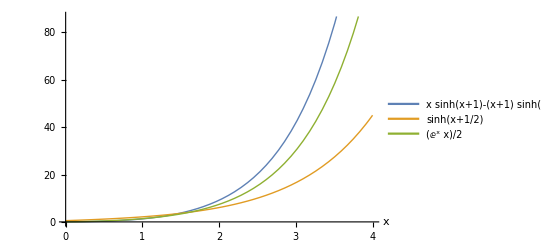

```mathematica
Clear[x]
basicStatMechProblemSet5Problem3Fig2A = Plot[ 
{
x Sinh[ x + 1] - (x+1) Sinh[x],
Sinh[x + 1/2],
x E^x/2(*,  
Sqrt[E]E^x/2*)
}, 
{x, 0, 4},
AxesLabel -> {x},
PlotStyle->Thick,
PlotLegends->Placed[{
x sinh[x + 1] - (x + 1)sinh[x], 
sinh[x+1/2], 
x E^x/2(*, 
 Sqrt[E] E^x/(2)*)
},Center]
]
```

```mathematica
Manipulate[
Plot[ 
{
Sinh[1/x]/(E^( a/x) + 1 + 2 Cosh[1/x])

(*,
Sinh[1/x]/(E^( a/x) + 1),
Sinh[1/x]/( 1 + 2 Cosh[1/x])*)
}
, 
{x, 0.001, 100},
PlotRange -> Full,
PlotStyle->Thick,
AxesLabel -> {Subscript[k, B] T/(μ ℏ ℰ) //fs, "<L_z>/2 ℏ"//fs}
]
, {{a, 16}, 0.001, 100}]
```

```mathematica
basicStatMechProblemSet5Problem3Fig3A = DynamicModule[{a=16},Plot[{Sinh[1/x]/(ⅇ^(a/x)+1+2 Cosh[1/x])},{x,0.001,100},PlotRange->Full,PlotStyle->Thick,AxesLabel->{fs[(Subscript[k, B] T)/(μ ℏ ℰ)],fs["<\!\(\*SubscriptBox[\(L\), \(z\)]\)>/2 ℏ"]}]]
```

```mathematica
Manipulate[
Plot[ 
{
Sinh[1/x]/(E^( a/x) + 1 + 2 Cosh[1/x])
, x/(4 x^2 + a x + 1)
, 1/(4 x)

}
, 
{x, 0.001, 100},
AxesLabel -> {Subscript[k, B] T/(μ ℏ ℰ) //fs},
PlotStyle->Thick
]
, {{a, 16}, 0.001, 100}]
```

```mathematica
basicStatMechProblemSet5Problem3Fig4A = DynamicModule[{a=16},Plot[{Sinh[1/x]/(ⅇ^(a/x)+1+2 Cosh[1/x]),x/(4 x^2+a x+1),1/(4 x)},{x,0.001,100},AxesLabel->{fs[(Subscript[k, B] T)/(μ ℏ ℰ)]},PlotStyle->Thick]]
```

```mathematica
Manipulate[
Plot[
{
1/ (1 + E^(a/t))
(*,  1/ (1 + E^(-a/t))*)
},{t,0,10}
],
{a, 1, 10}
]
```

```mathematica
basicStatMechProblemSet5Problem3Fig5A = DynamicModule[{a=3.58},Plot[{1/(1+ⅇ^(a/t))},{t,0,10}, PlotStyle->Thick]]
```

```mathematica
peeters`exportForLatex["basicStatMechProblemSet5Problem3Fig3A",basicStatMechProblemSet5Problem3Fig3A]
```

{basicStatMechProblemSet5Problem3Fig3A.eps,basicStatMechProblemSet5Problem3Fig3Apn.png}

```mathematica
peeters`exportForLatex["basicStatMechProblemSet5Problem3Fig4A",basicStatMechProblemSet5Problem3Fig4A]
```

{basicStatMechProblemSet5Problem3Fig4A.eps,basicStatMechProblemSet5Problem3Fig4Apn.png}

```mathematica
peeters`exportForLatex["basicStatMechProblemSet5Problem3Fig2A",basicStatMechProblemSet5Problem3Fig2A]
```

{basicStatMechProblemSet5Problem3Fig2A.eps,basicStatMechProblemSet5Problem3Fig2Apn.png}

```mathematica
peeters`exportForLatex["basicStatMechProblemSet5Problem3Fig5A",basicStatMechProblemSet5Problem3Fig5A]
```

{basicStatMechProblemSet5Problem3Fig5A.eps,basicStatMechProblemSet5Problem3Fig5Apn.png}